# HanoiTower Documentation Template

```mathematica
<<Deus`
```

```mathematica
$DocActive="Deus";
```

HanoiGraph

HanoiGraph[n]

HanoiGraph[n]给出n阶汉诺图

Details

HanoiGraph has 1 call pattern

HanoiGraph has an internal SubValues pattern

HanoiGraph has the following Attributes

Protected

ReadProtected

HanoiGraph is a formatted symbol

### Basic Examples

Load Deus.

Needs["Deus`"]

绘制 5 阶汉诺图.

HanoiGraph[5,GraphLayout→"SpringEmbedding"]

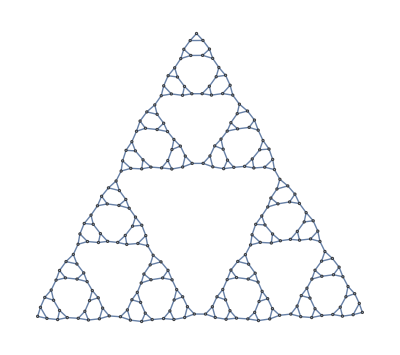

### Advance

汉诺图具有自相似结构.

HanoiGraph[#,GraphLayout→"SpringEmbedding"]&/@{1,2,3,4}//Multicolumn

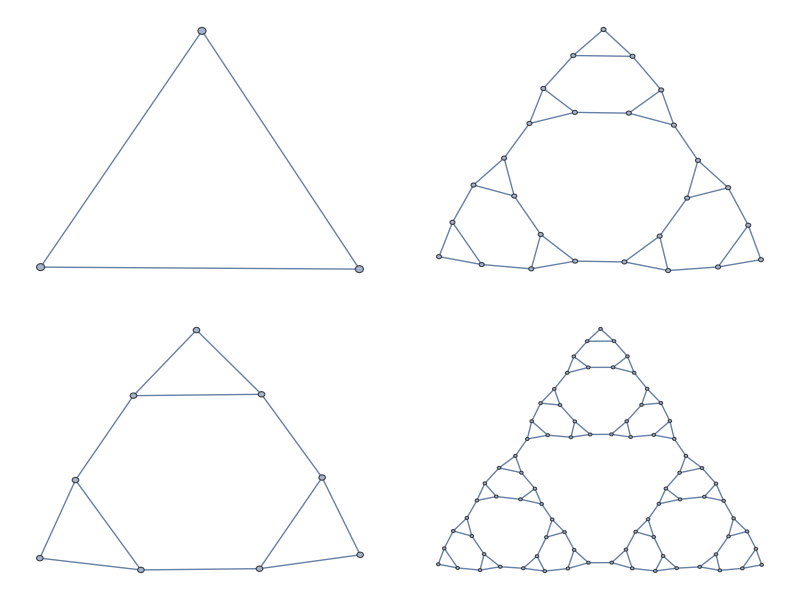

请不要输入巨大的整数n, 很可能导致前端奔溃, 因为节点数目指数级的增加.

gs=HanoiGraph/@Range[6];
VertexCount/@gs
EdgeCount/@gs

{3,9,27,81,243,729}

{3,12,39,120,363,1092}

Wolfram 数据库中有前五阶的汉诺图.

GraphData["Hanoi"]

{{"Hanoi",2},{"Hanoi",3},{"Hanoi",4},{"Hanoi",5},"TriangleGraph"}

#### Mathworld

更多性质详见Mathworld.

["Mathworld::HanoiGraph"](http://mathworld.wolfram.com/HanoiGraph.html)
["Mathworld::HanoiGraph/nb"](http://mathworld.wolfram.com/notebooks/GraphTheory/HanoiGraph.nb)

### Definitions

Examine all definitions:

GeneralUtilities`PrintDefinitionsLocal[Deus`HanoiGraph]

## See Also

HanoiGraph

HanoiSteps

HanoiMove

HanoiShow

HanoiTower

Related Guide

Deus Overview | Deus

HanoiTower Package | HanoiTowerPackage

Related Tutorials

Deus Tutorial | DeusTutorial

HanoiSteps

HanoiSteps[n, p]

给出汉诺塔的最少移动步骤, n>4 的情况尚未证明.

Details

HanoiSteps has 1 call pattern

HanoiSteps has an internal SubValues pattern

HanoiSteps has the following Attributes

Protected

ReadProtected

HanoiSteps is a formatted symbol

### Basic Examples

Load Deus:

Needs["Deus`"]

From HanoiSteps[n, p]:

HanoiSteps[4]

HanoiSteps[4]

### Definitions

Examine all definitions:

GeneralUtilities`PrintDefinitionsLocal[Deus`HanoiSteps]

## See Also

HanoiGraph

HanoiSteps

HanoiMove

HanoiShow

HanoiTower

Related Guide

Deus Overview | Deus

HanoiTower Package | HanoiTowerPackage

Related Tutorials

Deus Tutorial | DeusTutorial

HanoiMove

HanoiMove[n]

给出n个盘子的汉诺塔的最优移动方式.

HanoiMove[start, finish]

给出三柱汉诺塔状态间的最优移动方式.
请不要输入过于复杂的状态, 因为路径长度指数增加.

Details

HanoiMove has 2 call patterns

HanoiMove has an internal SubValues pattern

HanoiMove has the following Options

Deus`HanoiTower`Pillar

3

HanoiMove has the following Attributes

Protected

ReadProtected

HanoiMove is a formatted symbol

### Basic Examples

Load Deus:

Needs["Deus`"]

显示三柱汉诺塔四个盘子时的最优移动步骤

HanoiMove[4]//MatrixForm
Echo[%//Length,"最少移动步数: "];

({1,2,3,4} | {} | {}
{2,3,4} | {1} | {}
{3,4} | {1} | {2}
{3,4} | {} | {1,2}
{4} | {3} | {1,2}
{1,4} | {3} | {2}
{1,4} | {2,3} | {}
{4} | {1,2,3} | {}
{} | {1,2,3} | {4}
{} | {2,3} | {1,4}
{2} | {3} | {1,4}
{1,2} | {3} | {4}
{1,2} | {} | {3,4}
{2} | {1} | {3,4}
{} | {1} | {2,3,4}
{} | {} | {1,2,3,4})

最少移动步数:  16

### Advance

显示两个状态间的最优移动步骤.

start={{1,2},{3,4},{}};
finish={{2,3},{},{1,4}};
HanoiMove[start,finish]//MatrixForm
Echo[%//Length,"最少移动步数: "];

({1,2} | {3,4} | {}
{2} | {1,3,4} | {}
{} | {1,3,4} | {2}
{} | {3,4} | {1,2}
{3} | {4} | {1,2}
{3} | {1,4} | {2}
{2,3} | {1,4} | {}
{1,2,3} | {4} | {}
{1,2,3} | {} | {4}
{2,3} | {} | {1,4})

最少移动步数:  10

#### Options::Pillar

Pillar选项指明汉诺塔的柱数.

HanoiMove[4,Pillar -> 4]//MatrixForm
Echo[%//Length,"最少移动步数: "];

({1,2,3,4} | {} | {} | {}
{2,3,4} | {} | {} | {1}
{3,4} | {2} | {} | {1}
{3,4} | {1,2} | {} | {}
{4} | {1,2} | {3} | {}
{} | {1,2} | {3} | {4}
{} | {1,2} | {} | {3,4}
{1} | {2} | {} | {3,4}
{1} | {} | {} | {2,3,4}
{} | {} | {} | {1,2,3,4})

最少移动步数:  10

### Definitions

Examine all definitions:

GeneralUtilities`PrintDefinitionsLocal[Deus`HanoiMove]

## See Also

HanoiGraph

HanoiSteps

HanoiMove

HanoiShow

HanoiTower

Related Guide

Deus Overview | Deus

HanoiTower Package | HanoiTowerPackage

Related Tutorials

Deus Tutorial | DeusTutorial

HanoiShow

HanoiShow[states, OptionsPattern[]]

可视化圆盘的移动过程

Details

HanoiShow has 1 call pattern

HanoiShow has an internal SubValues pattern

HanoiShow has the following Options

Deus`HanoiTower`TableStyle

{RGBColor[0.6, 0.4, 0.2]}

Deus`HanoiTower`PillarStyle

{RGBColor[{41/51, 79/255, 6/85}]}

Deus`HanoiTower`DiskColor

ColorDataFunction[3, "Indexed", {1, 10, 1}, {RGBColor[0., 0., 0.], RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862], RGBColor[0.996078431372549, 0.9882352941176471, 0.03529411764705882], RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862], RGBColor[0.1450980392156863, 0.43529411764705883, 0.3843137254901961], RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824], RGBColor[0.15294117647058825, 0.11372549019607843, 0.49019607843137253], RGBColor[0.47058823529411764, 0.2627450980392157, 0.5843137254901961], RGBColor[0.8901960784313725, 0.011764705882352941, 0.49019607843137253], RGBColor[0.9058823529411765, 0.027450980392156862, 0.12941176470588237]}[[Mod[Floor[#1], 10, 1]]] & ]

HanoiShow has the following Attributes

Protected

ReadProtected

HanoiShow is a formatted symbol

### Basic Examples

Load Deus:

Needs["Deus`"]

From HanoiShow[states, OptionsPattern[]]:

HanoiShow[states]

### Advance

#### Options::TableStyle

HanoiShow[states, Deus`HanoiTower`TableStyle -> {RGBColor[0.6, 0.4, 0.2]}]

#### Options::PillarStyle

HanoiShow[states, Deus`HanoiTower`PillarStyle -> {RGBColor[{41/51, 79/255, 6/85}]}]

#### Options::DiskColor

HanoiShow[states, Deus`HanoiTower`DiskColor -> ColorDataFunction[3, "Indexed", {1, 10, 1}, {RGBColor[0., 0., 0.], RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862], RGBColor[0.996078431372549, 0.9882352941176471, 0.03529411764705882], RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862], RGBColor[0.1450980392156863, 0.43529411764705883, 0.3843137254901961], RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824], RGBColor[0.15294117647058825, 0.11372549019607843, 0.49019607843137253], RGBColor[0.47058823529411764, 0.2627450980392157, 0.5843137254901961], RGBColor[0.8901960784313725, 0.011764705882352941, 0.49019607843137253], RGBColor[0.9058823529411765, 0.027450980392156862, 0.12941176470588237]}[[Mod[Floor[#1], 10, 1]]] & ]]

### Definitions

Examine all definitions:

GeneralUtilities`PrintDefinitionsLocal[Deus`HanoiShow]

## See Also

HanoiGraph

HanoiSteps

HanoiMove

HanoiShow

HanoiTower

Related Guide

Deus Overview | Deus

HanoiTower Package | HanoiTowerPackage

Related Tutorials

Deus Tutorial | DeusTutorial

HanoiTower

HanoiTower

汉诺塔程序包, 包括可视化和最短路径等.

Details

HanoiTower has an internal SubValues pattern

HanoiTower has the following Attributes

Protected

ReadProtected

HanoiTower is a formatted symbol

### Basic Examples

Load Deus:

Needs["Deus`"]

### Definitions

Examine all definitions:

GeneralUtilities`PrintDefinitionsLocal[Deus`HanoiTower]

Defer[HanoiTower]

## See Also

HanoiGraph

HanoiSteps

HanoiMove

HanoiShow

HanoiTower

Related Guide

Deus Overview | Deus

HanoiTower Package | HanoiTowerPackage

Related Tutorials

Deus Tutorial | DeusTutorial